# Homework 3:

Part A:
A1:
a)

{ϵ→1.,σ→1.}

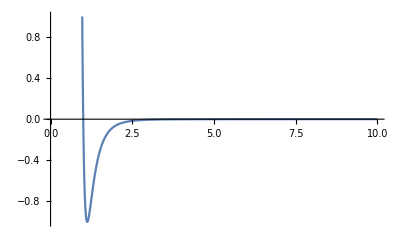

```mathematica
V[r_]=4ϵ((σ/r)^12-(σ/r)^6);
Subs = {ϵ -> 1.0,σ-> 1.0}
Plot[V[r] /. Subs, {r,0,10},PlotRange -> {-1,1}]
```

b)

```mathematica
V[r_]:=4ϵ((σ/r)^12-(σ/r)^6);
Subs = {ϵ -> 1.0,σ-> 1.0};
deriv := D[V[r] /. Subs,r];
optimal_distance = Solve[deriv == 0 ,r,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-1.12246},{r→1.12246}}

In the code above we specified for only real values of r since radius is a distance and cannot be complex. Therefore the minimum distance r  = 1.2246.

c)

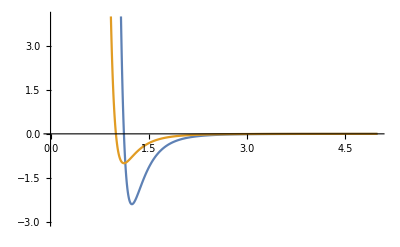

```mathematica
V[r_]:=4ϵ((σ/r)^12-(σ/r)^6);
Subs = {ϵ -> 1.0,σ-> 1.0};
Force[r_] = -D[V[r],r];
Plot[{Force[r]/.Subs,V[r]/.Subs},{r,0.1,5},PlotRange->{-3,4}]
```

d)

The force is positive, therefore the particles will move away from each other which will result in an increase in radius. Compared to the plot from part a) the potential is zero at a radius of 1 but the force is not. The force does not reach zero until the radius is about 1.1. The sign of the force is negative.

A2:
a)

```mathematica
Clear[x];
V[r_]:=4ϵ((σ/r)^12-(σ/r)^6);
Subs = {ϵ -> 1.0,σ-> 1.0,m->1};
Force[r_] = -D[V[r],r];
dt = 0.02;

time=10;
h=0.02;
nSteps=Round[time/h];
x0= 2.0;
v0=-0.1;
x[0]=x0;
x[1] = (x0+1/2Force[x[0]]/m dt^2)/.Subs;
v[0] = v0;
```

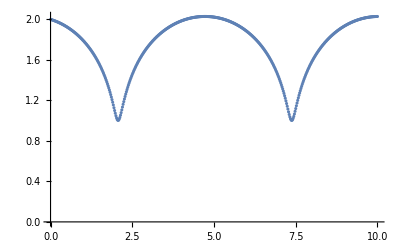

```mathematica
Do[
x[n+1] = x[n]+v[n]*h+Force[x[n]]*h*h/(2*m) /.Subs;
v[n+1] = v[n]+h*(Force[x[n]]+Force[x[n+1]])/(2*m)/.Subs;
,{n,0,nSteps}]
xData=Table[{n dt,x[n]},{n,0,nSteps}];
xPlot=ListPlot[xData];
Show[xPlot]
```

b)

The point is curved for small r due to a high forces acting on the object. Compared to a larger r the forces acting on the object does not impact the system as severely.

A3:
a)

E = K + V = 1/2 MV[n]^2 + V[x[n]] , for mass we assume the particle as a mass of 1.

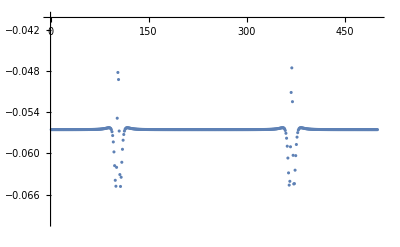

```mathematica
time=10;
h=0.02;
nSteps=Round[time/h];
V[r_]:=4ϵ((σ/r)^12-(σ/r)^6);
Subs = {ϵ -> 1.0,σ-> 1.0,m->1};
Vsubs[r_] = V[r] /.Subs;
ListPlot[Table[Vsubs[x[n]]+(1/2)*v[n]*v[n],{n,nSteps}],PlotRange-> {-0.07,-0.04},PlotLegends->"E(n)"]
```

b)

```mathematica
h = 0.01;
n=0;

Do [
x[n+1] = x[n]+v[n]*h+Force[x[n]]*h*h/(2 m)/.Subs;
v[n+1] = v[n]+h*(Force[x[n]]+Force[x[n+1]])/(2 m)/.Subs;
{n,0,nSteps}
]
ListPlot[Table[Vsubs[x[n]]+(1/2)*v[n]*v[n],{n,nSteps}],PlotRange-> {-0.07,-0.04}]
```

-Graphics-

c)

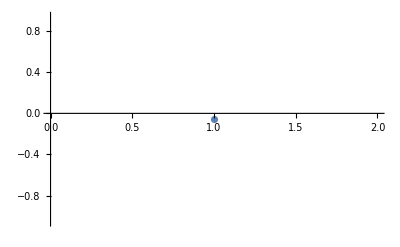

```mathematica
Clear[x];
V[r_]:=4ϵ((σ/r)^12-(σ/r)^6);
Subs = {ϵ -> 1.0,σ-> 1.0,m->1};
Force[r_] = -D[V[r],r];
dt = 0.02;

time=10;
h=0.02;
nSteps=Round[time/h];
x0= 2.0;
v0=-0.1;
x[0]=x0;
x[1] = (x0+1/2Force[x[0]]/m dt^2)/.Subs;
v[0] = v0;
h = 0.01;
n=0;

Do [
x[n+1] = x[n]+v[n]*h+Force[x[n]]*h*h/(2 m)/.Subs;
v[n+1] = v[n]+h*(Force[x[n]]+Force[x[n+1]])/(2 m)/.Subs;
{n,nSteps}
]
ListPlot[Table[Vsubs[x[n]]+(1/2)*v[n]*v[n],{n,nSteps}],PlotRange->{10,-10}]
```

Part B:
B1:
a)

-Graphics3D-

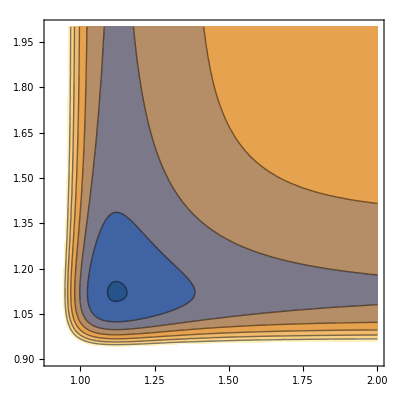

```mathematica
Vlj[r_]=4ϵ((σ/r)^12-(σ/r)^6);
Flj[r_]=24ϵ(2(σ^12/r^13)-(σ^6/r^7));
Subs={ϵ->1,σ->1,m->1};
V[rAB_,rBC_]=Vlj[rAB]+Vlj[rAB+rBC]+Vlj[rBC] /.Subs;
Plot3D[V[rAB,rBC]/.Subs,{rAB,0,0.9},{rBC,0.9,2.0}]
VPlot = ContourPlot[V[rAB,rBC]/.Subs,{rAB,0.9,2.0},{rBC,0.9,2.0}]
```

b)

200

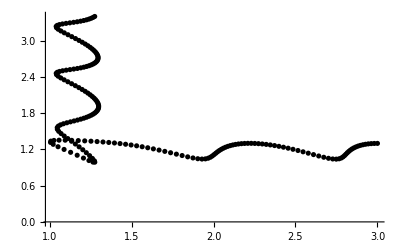

```mathematica
time=4.0;
h=0.02;
nSteps=Round[time/h]
Clear[fA,fB,fC]
xA[0]=-3.0;
xB[0]=0.0;
xC[0]=1.3;
vA[0]=1.0;
vB[0]=0;
vC[0]=0;
fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]]/.Subs;
fB[0]=-Flj[xC[0]-xB[0]]+Flj[xB[0]-xA[0]]/.Subs;
fC[0]=Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]]/.Subs;
Do[
xA[n+1]= xA[n]+vA[n]h +h^2 fA[n]/(2m)/.Subs;
xB[n+1]= xB[n]+vB[n]h +h^2 fB[n]/(2m)/.Subs;
xC[n+1]= xC[n]+vC[n]h +h^2 fC[n]/(2m)/.Subs;
fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]]/.Subs;
fB[n+1]=-Flj[xC[n+1]-xB[n+1]]+Flj[xB[n+1]-xA[n+1]]/.Subs;
fC[n+1]=Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]]/.Subs;
vA[n+1]=vA[n]+h(fA[n]+fA[n+1])/(2m)/.Subs;
vB[n+1]=vB[n]+h(fB[n]+fB[n+1])/(2m)/.Subs;
vC[n+1]=vC[n]+h(fC[n]+fC[n+1])/(2m)/.Subs;
,{n,0,nSteps}]
rData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
rPlot=ListPlot[rData,PlotStyle->Black]
```

The initial conditions chosen here correspond to particle A starting from rest and colliding with particle B which then collides with particle C.

c)

750

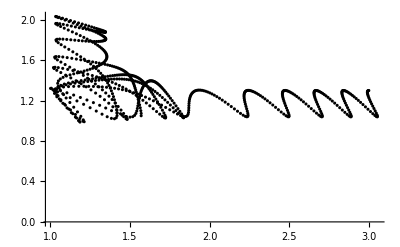

```mathematica
time=15.0;
h=0.02;
nSteps=Round[time/h]
Clear[fA,fB,fC]
xA[0]=-3.0;
xB[0]=0.0;
xC[0]=1.3;
vA[0]=0.2;
vB[0]=0;
vC[0]=0;
fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]]/.Subs;
fB[0]=-Flj[xC[0]-xB[0]]+Flj[xB[0]-xA[0]]/.Subs;
fC[0]=Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]]/.Subs;
Do[
xA[n+1]= xA[n]+vA[n]h +h^2 fA[n]/(2m)/.Subs;
xB[n+1]= xB[n]+vB[n]h +h^2 fB[n]/(2m)/.Subs;
xC[n+1]= xC[n]+vC[n]h +h^2 fC[n]/(2m)/.Subs;
fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]]/.Subs;
fB[n+1]=-Flj[xC[n+1]-xB[n+1]]+Flj[xB[n+1]-xA[n+1]]/.Subs;
fC[n+1]=Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]]/.Subs;
vA[n+1]=vA[n]+h(fA[n]+fA[n+1])/(2m)/.Subs;
vB[n+1]=vB[n]+h(fB[n]+fB[n+1])/(2m)/.Subs;
vC[n+1]=vC[n]+h(fC[n]+fC[n+1])/(2m)/.Subs;
,{n,0,nSteps}]
rData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
rPlot=ListPlot[rData,PlotStyle->Black]
```

d)

250

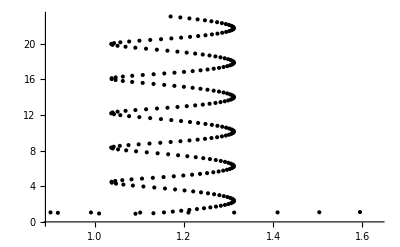

```mathematica
time=5.0;
h=0.02;
nSteps=Round[time/h]
Clear[fA,fB,fC]
xA[0]=-3.0;
xB[0]=0.0;
xC[0]=1.3;
vA[0]=5.0;
vB[0]=0;
vC[0]=0;
fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]]/.Subs;
fB[0]=-Flj[xC[0]-xB[0]]+Flj[xB[0]-xA[0]]/.Subs;
fC[0]=Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]]/.Subs;
Do[
xA[n+1]= xA[n]+vA[n]h +h^2 fA[n]/(2m)/.Subs;
xB[n+1]= xB[n]+vB[n]h +h^2 fB[n]/(2m)/.Subs;
xC[n+1]= xC[n]+vC[n]h +h^2 fC[n]/(2m)/.Subs;
fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]]/.Subs;
fB[n+1]=-Flj[xC[n+1]-xB[n+1]]+Flj[xB[n+1]-xA[n+1]]/.Subs;
fC[n+1]=Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]]/.Subs;
vA[n+1]=vA[n]+h(fA[n]+fA[n+1])/(2m)/.Subs;
vB[n+1]=vB[n]+h(fB[n]+fB[n+1])/(2m)/.Subs;
vC[n+1]=vC[n]+h(fC[n]+fC[n+1])/(2m)/.Subs;
,{n,0,nSteps}]
rData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
rPlot=ListPlot[rData,PlotStyle->Blue]
```

Part C:
C1:
a)

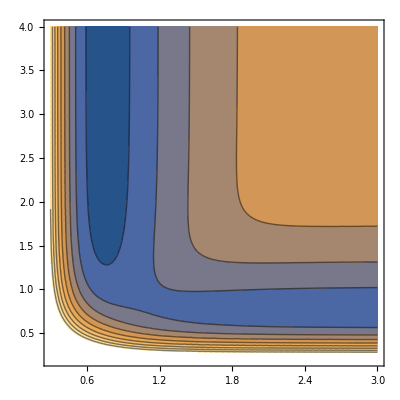

```mathematica
Clear[Vleps,qAB,qBC,qAC,jAB,jBC,jAC]
dAB=4.746 ;            (* the well depth in eV of the AB interaction *)
dBC=4.746 ;            (*      -                      BC      -      *)
dAC=3.445 ;            (*      -                      AC      -      *)
r0AB=0.742 ;         (* the bond distance in Angstrom for the AB dimer *)
r0BC=0.742 ;         (*            -                          BC   -   *)
r0AC=0.742 ;          (*            -                          AC   -   *)
alphaAB=1.942 ;   (* the exponential decay length of AB interaction *)
alphaBC=1.942 ;  (*         -                       BC      -      *)
alphaAC=1.942 ;  (*         -                       AC      -      *)
ap1=1.05 ;               (* This is written as (1+a) in the lecture notes *)
bp1=1.30 ;               (*        -           (1+b)          -           *) 
cp1=1.05;                (*        -           (1+c)          -           *)

qAB[r_] =  dAB/4 (3 Exp[-2 alphaAB (r-r0AB)] - 2 Exp[- alphaAB (r-r0AB)]);
qBC[r_] =  dBC/4 (3 Exp[-2 alphaBC (r-r0BC)] - 2 Exp[- alphaBC (r-r0BC)]);
qAC[r_] =  dAC/4 (3 Exp[-2 alphaAC (r-r0AC)] - 2 Exp[- alphaAC (r-r0AC)]);

jAB[r_] =  dAB/4 (Exp[-2 alphaAB (r-r0AB)] - 6 Exp[- alphaAB (r-r0AB)]);
jBC[r_] =  dBC/4 (Exp[-2 alphaBC (r-r0BC)] - 6 Exp[- alphaBC (r-r0BC)]);
jAC[r_] =  dAC/4 (Exp[-2 alphaAC (r-r0AC)] - 6 Exp[- alphaAC (r-r0AC)]);

Vleps[r1_,r2_] =  qAB[r1]/ap1 + qBC[r2]/bp1 + qAC[r1+r2]/cp1 -
                   Sqrt[(jAB[r1]/ap1)^2 + (jBC[r2]/bp1)^2 + (jAC[r1+r2]/cp1)^2 -
                         jAB[r1] jBC[r2]/(ap1 bp1) - jBC[r2] jAC[r1+r2]/(bp1 cp1)-
                         jAB[r1] jAC[r1+r2] /(ap1 cp1)] ;
ContourPlot[Vleps[r1,r2],{r1,0.3,3.0},{r2,0.2,4.0}]
```

the lower potential is spread out more on r2 compared to the potential in part b.

b)

```mathematica
Fa[r1_,r2_]= D[Vleps[r1,r2],r1];
Fb[r1_,r2_]= -D[Vleps[r1,r2],r1]+D[Vleps[r1,r2],r2];
Fc[r1_,r2_]= -D[Vleps[r1,r2],r2];
```

C)

```mathematica
Subs = {ϵ -> 1.0,σ-> 1.0,m->1};
time=5.0;
h=0.02;
nSteps=Round[time/h]
Clear[fA,fB,fC]
xA[0]=-3.0;
xB[0]=0.0;
xC[0]=0.8;
vA[0]=1.0;
vB[0]=0.0;
vC[0]=0.0;
Do[
xA[n+1]= xA[n]+vA[n]h +h^2 Fa[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
xB[n+1]= xB[n]+vB[n]h +h^2 Fb[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
xC[n+1]= xC[n]+vC[n]h +h^2 Fc[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
vA[n+1]=vA[n]+h(Fa[xB[n]-xA[n],xC[n]-xB[n]]+Fa[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
vB[n+1]=vB[n]+h(Fb[xB[n]-xA[n],xC[n]-xB[n]]+Fb[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
vC[n+1]=vC[n]+h(Fc[xB[n]-xA[n],xC[n]-xB[n]]+Fc[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
,{n,0,nSteps}]
rData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
rPlot=ListPlot[rData,PlotStyle->Red]
```

d)

```mathematica
Subs = {ϵ -> 1.0,σ-> 1.0,m->1};
time=5.0;
h=0.02;
nSteps=Round[time/h]
Clear[fA,fB,fC]
xA[0]=-3.0;
xB[0]=0.0;
xC[0]=0.8;
vA[0]=1.5;
vB[0]=0.0;
vC[0]=0.0;
Do[
xA[n+1]= xA[n]+vA[n]h +h^2 Fa[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
xB[n+1]= xB[n]+vB[n]h +h^2 Fb[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
xC[n+1]= xC[n]+vC[n]h +h^2 Fc[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
vA[n+1]=vA[n]+h(Fa[xB[n]-xA[n],xC[n]-xB[n]]+Fa[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
vB[n+1]=vB[n]+h(Fb[xB[n]-xA[n],xC[n]-xB[n]]+Fb[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
vC[n+1]=vC[n]+h(Fc[xB[n]-xA[n],xC[n]-xB[n]]+Fc[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
,{n,0,nSteps}]
rData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
rPlot=ListPlot[rData,PlotStyle->Blue]


Subs = {ϵ -> 1.0,σ-> 1.0,m->1};
time=5.0;
h=0.02;
nSteps=Round[time/h]
Clear[fA,fB,fC]
xA[0]=-3.0;
xB[0]=0.0;
xC[0]=0.8;
vA[0]=1.0;
vB[0]=0.0;
vC[0]=0.0;
Do[
xA[n+1]= xA[n]+vA[n]h +h^2 Fa[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
xB[n+1]= xB[n]+vB[n]h +h^2 Fb[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
xC[n+1]= xC[n]+vC[n]h +h^2 Fc[xB[n]-xA[n],xC[n]-xB[n]]/(2m)/.Subs;
vA[n+1]=vA[n]+h(Fa[xB[n]-xA[n],xC[n]-xB[n]]+Fa[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
vB[n+1]=vB[n]+h(Fb[xB[n]-xA[n],xC[n]-xB[n]]+Fb[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
vC[n+1]=vC[n]+h(Fc[xB[n]-xA[n],xC[n]-xB[n]]+Fc[xB[n+1]-xA[n+1],xC[n+1]-xB[n+1]])/(2m)/.Subs;
,{n,0,nSteps}]
rData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
rPlot=ListPlot[rData,PlotStyle->Black]
```

The condition where the initial velocity of particle A is the highest is most likely to increase reaction probability.

D)
based on the location of the saddle points it can be concluded that increasing the translational energy will increase the reaction probability.